```mathematica
BisectionMethod[Start_, Func_,Tol_]:=Module[{St=Start,f=Func,TOL=Tol},
OppSigns[{x_,y_}]:=TrueQ[f[x]f[y]≤ 0];
Test[{x_,y_}]:=TrueQ[Abs[(x-y)]/2≥TOL];
GetInt[{x_,y_}]:=If[f[x]==0,Return[{x-TOL/2,x+TOL/2}],If[f[y]==0,Return[{y-TOL/2,y+TOL/2}],If[f[(x+y)/2]==0,Return[{(x+y)/2-TOL/2,(x+y)/2+TOL/2}],If[Select[{{x,(x+y)/2},{(x+y)/2,y}},OppSigns]=={},Throw["Bad Interval"],Select[{{x,(x+y)/2},{(x+y)/2,y}},OppSigns][[1]]]]]];

Int=Catch[NestWhileList[GetInt,Start,Test,1,50]];
If[Int=="Bad Interval",Return["Bad Interval"],{}];
Table[(Int[[i,1]]+Int[[i,2]])/2,{i,1,Length[Int]}]
];
```

```mathematica
NewtonsMethod[p0_,Func_,FuncP_,Tol_]:=Module[{f=Func,fp=FuncP},
Test[x_,y_]:=TrueQ[Abs[x-y]≥ Tol];
g[x_]:=x-f[x]/fp[x];
NestWhileList[g,p0,Test,2,100]
];
```

```mathematica
SecantMethod[p0_,Func_,Tol_]:=Module[{f=Func},
Test[{x_,y_}]:=TrueQ[Abs[x-y]≥ Tol];
g[{x_,y_}]:={y,x-(f[x](x-y))/(f[x]-f[y])};
App=NestWhileList[g,p0,Test,1,50];
Table[App[[i,2]],{i,1,Length[App]}]
(*App//Last//Last*)
];
```

# Convergence of Root Finders

Now that we have discussed three methods of root finding let’s compare how quickly they produce accurate results.

Let’s first collect some data by running the three methods to approximate π.

```mathematica
SM=SetPrecision[SecantMethod[{21/7,23/7},Sin[#]&,10^(-10)],300];
```

```mathematica
NM=SetPrecision[NewtonsMethod[23/7,Sin[#]&,Cos[#]&,10^(-10)],300];
```

```mathematica
BM=SetPrecision[BisectionMethod[{21/7,23/7},Sin[#]&,10^(-10)],300];
```

This is a neat trick to estimate the number of digits an approximation is correct to. The idea is to take the log base 10 of the difference between the approximation and the actual value.

```mathematica
CorrectDigits[Approx_,Actual_]:=Abs[Log10[SetPrecision[Abs[Approx - Actual],300]]];
```

Let’s try it out!

```mathematica
N[22/7]
N[π]
N[22/7]-N[π]
```

3.14286

3.14159

0.00126449

```mathematica
N[CorrectDigits[22/7,π],1]
```

3.

We can now make tables of the number of correct digits at each iteration of our three root finder.

```mathematica
BMD=Table[CorrectDigits[BM[[i]],Pi],{i,1,Length[BM]}];
```

```mathematica
NMD=Table[CorrectDigits[NM[[i]],Pi],{i,1,Length[NM]}];
```

```mathematica
SMD=Table[CorrectDigits[SM[[i]],Pi],{i,1,Length[SM]}];
```

Now that we have the numbers of correct digits we can compare them graphically.

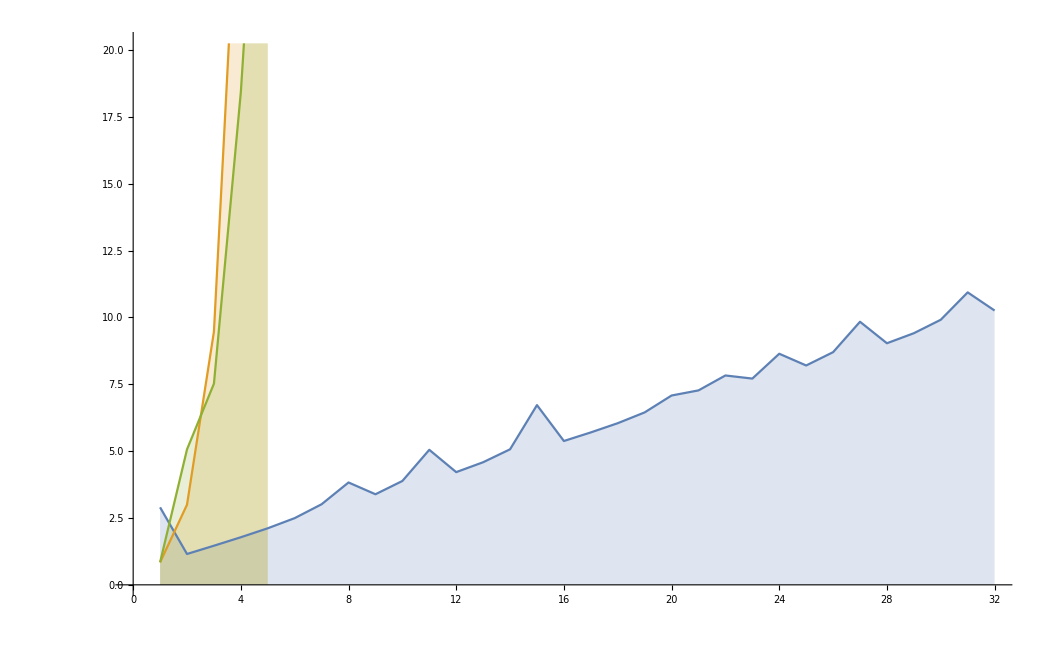

```mathematica
ListLinePlot[{BMD,NMD,SMD},Filling->Axis]
```

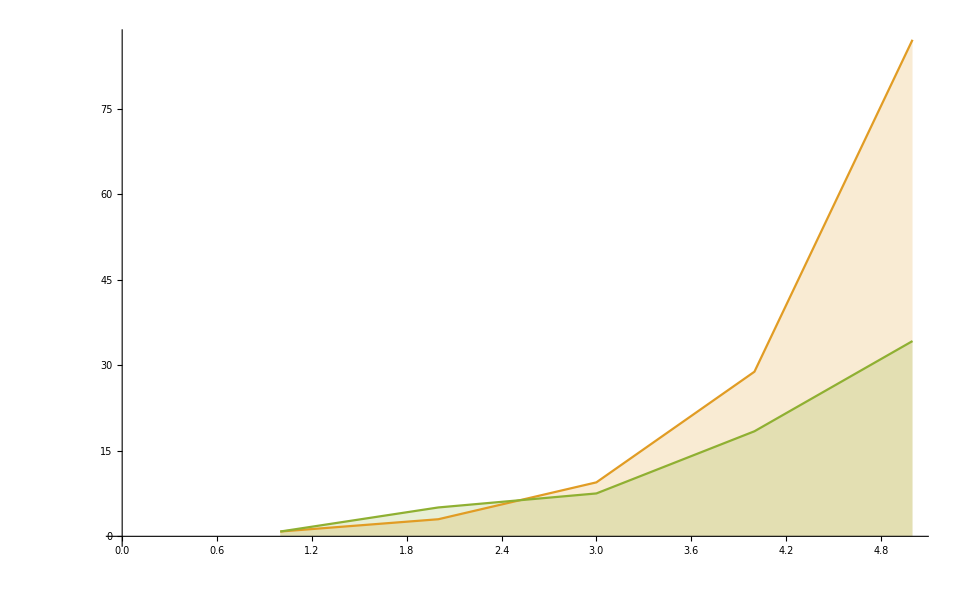

```mathematica
ListLinePlot[{{0},NMD,SMD},Filling->Axis]
```

Notice that we can see the orders of convergence in this graph. Since the bisection method is linearly convergent the number of correct digits grows (roughly) linearly. Newton’s Method converges quadratically and the secant method converges almost quadratically (see below), so their numbers of correct digits grow (roughly) exponentially.

We won’t prove this, but it turns out that the secant method converges with rate α=ϕ, the golden ratio!